# Uniform

```mathematica
dist=UniformDistribution[{0,max}]
```

UniformDistribution[{0,max}]

```mathematica
PDF[dist,z]
```

Piecewise[{{1/max, 0≤z≤max}, {0, True}}]

```mathematica
CDF[dist,z]
```

Piecewise[{{z/max, 0≤z≤max}, {1, z>max}, {0, True}}]

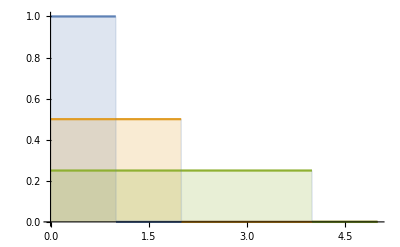

```mathematica
Plot[Table[PDF[UniformDistribution[{0,max}],x],{max,{1,2,4}}]//Evaluate,{x,0,5},PlotRange->All,Filling->Axis]
```

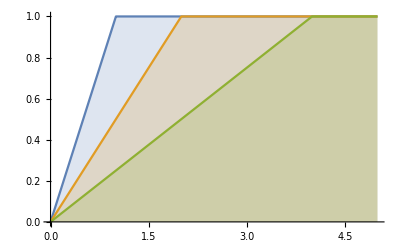

```mathematica
Plot[Table[CDF[UniformDistribution[{0,max}],x],{max,{1,2,4}}]//Evaluate,{x,0,5},Filling->Axis,Exclusions->None]
```

```mathematica
Mean[dist]
```

max/2

```mathematica
Median[dist]
```

max/2

```mathematica
Variance[dist]
```

max^2/12

```mathematica
StandardDeviation[dist]
```

max/(2 √3)

```mathematica
Skewness[dist]
```

0

```mathematica
Kurtosis[dist]
```

9/5

```mathematica
CharacteristicFunction[dist,t]
```

-(ⅈ (-1+ⅇ^(ⅈ max t)))/(max t)

```mathematica
Random[UniformDistribution[]]
```

0.864003